```mathematica
Quit[];
```

```mathematica
testFileName=FileNameJoin[{DirectoryName[NotebookDirectory[],1],FileBaseName[NotebookFileName[]]<>".wlt"}]
pacletDir=DirectoryName[testFileName,2]
PacletDirectoryLoad[pacletDir]
testContextBase=FileBaseName[testFileName]
$ContextPath=Cases[$ContextPath,Except["PacletizedResourceFunctions`"]]
```

/Users/fernandoduarte/Dropbox (Personal)/MyPackages/LongRunRisk/Tests/SolveEulerEq.wlt

/Users/fernandoduarte/Dropbox (Personal)/MyPackages/LongRunRisk/

{/Users/fernandoduarte/Dropbox (Personal)/MyPackages/LongRunRisk/}

SolveEulerEq

{Wolfram`Chatbook`,System`,Global`}

### CI Tests

```mathematica
If[FileNames[testFileName]==={},Nothing,DeleteFile[testFileName]]
```

```mathematica
confirm=False;
testContext="FernandoDuarte`LongRunRisk`ComputationalEngine`"<>testContextBase<>"`"
```

```mathematica
Begin["ComputationalEngine`EulerEq`"]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
Get["FernandoDuarte`LongRunRisk`Model`Catalog`"];
Needs["FernandoDuarte`LongRunRisk`Model`ProcessModels`"];
(*Needs["PacletizedResourceFunctions`"];*)
,"ConfirmResults"->confirm]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
Needs["FernandoDuarte`LongRunRisk`ComputationalEngine`SolveEulerEq`"];
,"ConfirmResults"->False]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
(*should be true if uncondE can be found*)
	Not[Names["*eulereq"]==={}]
,"ConfirmResults"->False]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
	mm=models;
	ms=KeySelect[mm,MatchQ[#,"BKY"|"NRC"|"BS" | "DES" | "WCratio"]&];
	msp=processModels[ms];
	modBKY=msp["BKY"];
	modNRC=msp["NRC"];
	modBS=msp["BS"];
	modDES=msp["DES"];
	modWCratio=msp["WCratio"];
	
	modBKYa=Map[Activate,modBKY];
	modNRCa=Map[Activate,modNRC];
	modBSa=Map[Activate,modBS];
	modDESa=Map[Activate,modDES];
	modWCratioa=Map[Activate,modWCratio];
,"ConfirmResults"->False]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
model=modBSa;
modelAssumptions=model["modelAssumptions"];
parameters=model["parameters"];
numStocks=model["numStocks"];

ratiosUncondERule={FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`Ewc->Simplify@FernandoDuarte`LongRunRisk`ComputationalEngine`ComputeUnconditionalExpectations`uncondE[wc[t],model],FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`Epd[j_]->Simplify@FernandoDuarte`LongRunRisk`ComputationalEngine`ComputeUnconditionalExpectations`uncondE[pd[t,j],model]}

,"ConfirmResults"->False]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
(* create system of equations for coefficients of wc ratio *)
{systemWc,unknownsWc}=findEulerEqConstants[retc[t+1],model]/.ratiosUncondERule;
(* create system of equations for coefficients of pd ratios *)
{systemPd,unknownsPd}=findEulerEqConstants[ret[t+1,j],model]/.ratiosUncondERule;

unknownsWcGuess=Prepend[Table[0,Length[unknownsWc]-1],8];
solWc=FindRoot[systemWc//.parameters,Thread@List[unknownsWc,unknownsWcGuess],MaxIterations->3500(*,PrecisionGoal->$MachinePrecision,AccuracyGoal->$MachinePrecision,WorkingPrecision->$MachinePrecision*)];

unknownsPdGuess=Prepend[Table[0,Length[unknownsPd]-1],7];
solOnePd[stockNumber_]:=FindRoot[systemPd/.j->stockNumber//.solWc//.parameters,Thread@List[unknownsPd,unknownsPdGuess]/.j->stockNumber,MaxIterations->3500(*,PrecisionGoal->$MachinePrecision,AccuracyGoal->$MachinePrecision,WorkingPrecision->$MachinePrecision*)];
solPd=solOnePd[#]&/@Range[numStocks];

bondRecursion = findBondRecursion[t,n+1,model]/.ratiosUncondERule;

maxMaturity=6;
bondCoefficientRules=Join[bondRecursion[[1,4]],bondRecursion[[2,4]]]/.(x_[n][j_Integer]:>Rule[x[n_][j],Symbol[(SymbolName@x)<>IntegerString[j]][n]]);
(*add small perturbation to make all coefficients depend on n, otherwise RecurrenceTable does not work*)
posConstantCoeff=Position[bondRecursion[[1,2]],_?(FreeQ[#,n-1]&),1,Heads->False];
perturbationNom=If[posConstantCoeff==={},0,10^-18 First@Extract[bondRecursion[[2,4]],posConstantCoeffNom]/.(n->n-1)];(*(Last@bondRecursion[[1,4]] /.n->n-1)*)
bondRecursionPerturbation=MapAt[(#/.(Equal[a_,b_]:>Equal[a,b+perturbation])&),bondRecursion[[1,2]],posConstantCoeff];
solBondNum=RecurrenceTable[Simplify[(Flatten[{bondRecursionPerturbation,bondRecursion[[1,3]]}]//.parameters/.solWc/.bondCoefficientRules)],bondRecursion[[1,4]]/.bondCoefficientRules,{n,1,maxMaturity},DependentVariables->Automatic]//Column//Chop;
solBond=Flatten[{bondRecursion[[1,3]]/. Equal->Rule,Table[Thread[bondRecursion[[1,4]]->solBondNum[[1,n]]],{n,1,maxMaturity}]}];
posConstantCoeffNom=Position[bondRecursion[[2,2]],_?(FreeQ[#,n-1]&),1,Heads->False];
perturbationNom=If[posConstantCoeffNom==={},0,10^-18 First@Extract[bondRecursion[[2,4]],posConstantCoeffNom]/.(n->n-1)];(*(Last@bondRecursion[[1,4]] /.n->n-1)*)
bondRecursionPerturbationNom=MapAt[(#/.(Equal[a_,b_]:>Equal[a,b+perturbationNom])&),bondRecursion[[2,2]],posConstantCoeffNom];
solNomBondNum=RecurrenceTable[Flatten[{bondRecursionPerturbationNom,bondRecursion[[2,3]]}]//.parameters/.solWc/.bondCoefficientRules,bondRecursion[[2,4]]/.bondCoefficientRules,{n,1,maxMaturity},DependentVariables->Automatic]//Column//Chop;
solNomBond=Flatten[{bondRecursion[[2,3]]/. Equal->Rule,Table[Thread[bondRecursion[[2,4]]->solNomBondNum[[1,n]]],{n,1,maxMaturity}]}];
,"ConfirmResults"->False]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
(*solutions to all coefficients are numbers*)
And@@(NumberQ/@(Values@Flatten@{solWc,solPd,solBond,solNomBond}))
,"ConfirmResults"->False]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
(*no time-varying variables in wc ratio coefficients*)
And@@{
FreeQ[findEulerEqConstants[retc[t+1],model],t],
FreeQ[findEulerEqConstants[retc[t],model],t]
}
,"ConfirmResults"->False]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
(*constants for wc ratio are independent of time period*)
And@@{
Simplify@Expand@(findEulerEqConstants[retc[t+1],model](*//.parameters*))===Simplify@Expand@(findEulerEqConstants[retc[t],model](*//.parameters*)),
Simplify@Expand@(findEulerEqConstants[ret[t+1,j],model](*//.parameters*))===Simplify@Expand@(findEulerEqConstants[ret[t,j],model](*//.parameters*))
}
,"ConfirmResults"->False]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
And@@{
(*unknowns in Euler eq for retc are in context "FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`"*)
And@@{
And@@(MatchQ["FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`",#]&/@(Context/@Head/@unknownsWc)),
And@@(MatchQ["FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`",#]&/@(Context/@Head/@Head/@unknownsPd))
},

And@@{
(*each equation evaluates to True or False when evaluated numerically*)
And@@(BooleanQ/@(systemWc//.parameters/.Thread[unknownsWc->Prepend[Table[0,Length[unknownsWc]-1],6]])),
And@@(BooleanQ/@(systemPd/.Thread[unknownsPd->Prepend[Table[0,Length[unknownsPd]-1],6]]/.j->1//.parameters/.Thread[unknownsWc->Prepend[Table[0,Length[unknownsWc]-1],6]])),
(*right hand side of each equation evaluates to a number*)
And@@(NumberQ/@(systemWc[[;;,2]]//.parameters/.Thread[unknownsWc->Prepend[Table[0,Length[unknownsWc]-1],6]])),
And@@(NumberQ/@(systemPd[[;;,2]]/.Thread[unknownsPd->Prepend[Table[0,Length[unknownsPd]-1],6]]/.j->1//.parameters/.Thread[unknownsWc->Prepend[Table[0,Length[unknownsWc]-1],6]])),

(*with random values of wc, pd coefficients*)
(*each equation evaluates to True or False when evaluated numerically*)
And@@(BooleanQ/@(systemWc//.parameters/.Thread[unknownsWc->Prepend[RandomReal[{-10,10},Length[unknownsWc]-1],6]])),
And@@(BooleanQ/@(systemPd/.Thread[unknownsPd->Prepend[RandomReal[{-10,10},Length[unknownsPd]-1],6]]/.j->1//.parameters/.Thread[unknownsWc->Prepend[RandomReal[{-10,10},Length[unknownsWc]-1],6]])),
(*right hand side of each equation evaluates to a number*)
And@@(NumberQ/@(systemWc[[;;,2]]//.parameters/.Thread[unknownsWc->Prepend[RandomReal[{-10,10},Length[unknownsWc]-1],6]])),
And@@(NumberQ/@(systemPd[[;;,2]]/.Thread[unknownsPd->Prepend[RandomReal[{-10,10},Length[unknownsPd]-1],6]]/.j->1//.parameters/.Thread[unknownsWc->Prepend[RandomReal[{-10,10},Length[unknownsWc]-1],6]]))
}
}
,"ConfirmResults"->False]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
And@@{
(*unknowns in Euler eq for retc are in context "FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`"*)
And@@{
And@@(MatchQ["FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`",#]&/@(Context/@Head/@Head/@bondRecursion[[1,4]])),
And@@(MatchQ["FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`",#]&/@(Context/@Head/@Head/@bondRecursion[[2,4]]))
},

And@@{
(*each equation evaluates to True or False when evaluated numerically*)
And@@(BooleanQ/@(Flatten[{bondRecursion[[1,2]],bondRecursion[[1,3]]}]//.parameters/.Thread[unknownsWc->Prepend[Table[0,Length[unknownsWc]-1],6]]/.(Thread[bondRecursion[[1,4]]->0]/.n->__) )),
And@@(BooleanQ/@(Flatten[{bondRecursion[[2,2]],bondRecursion[[2,3]]}]//.parameters/.Thread[unknownsWc->Prepend[Table[0,Length[unknownsWc]-1],6]]/.(Thread[bondRecursion[[2,4]]->0]/.n->__) )),
(*right hand side of each equation evaluates to a number*)
And@@(NumberQ/@(Flatten[{bondRecursion[[1,2]][[;;,2]],bondRecursion[[1,3]][[;;,2]]}]//.parameters/.Thread[unknownsWc->Prepend[Table[0,Length[unknownsWc]-1],6]]/.(Thread[bondRecursion[[1,4]]->0]/.n->__) )),
And@@(NumberQ/@(Flatten[{bondRecursion[[2,2]][[;;,2]],bondRecursion[[2,3]][[;;,2]]}]//.parameters/.Thread[unknownsWc->Prepend[Table[0,Length[unknownsWc]-1],6]]/.(Thread[bondRecursion[[2,4]]->0]/.n->__) )),

(*with random values of wc coefficient*)
(*each equation evaluates to True or False when evaluated numerically*)
And@@(BooleanQ/@(Flatten[{bondRecursion[[1,2]],bondRecursion[[1,3]]}]//.parameters/.Thread[unknownsWc->Prepend[RandomReal[{-10,10},Length[unknownsWc]-1],6]]/.(Thread[bondRecursion[[1,4]]->0]/.n->__) )),
And@@(BooleanQ/@(Flatten[{bondRecursion[[2,2]],bondRecursion[[2,3]]}]//.parameters/.Thread[unknownsWc->Prepend[RandomReal[{-10,10},Length[unknownsWc]-1],6]]/.(Thread[bondRecursion[[2,4]]->0]/.n->__) )),
(*right hand side of each equation evaluates to a number*)
And@@(NumberQ/@(Flatten[{bondRecursion[[1,2]][[;;,2]],bondRecursion[[1,3]][[;;,2]]}]//.parameters/.Thread[unknownsWc->Prepend[RandomReal[{-10,10},Length[unknownsWc]-1],6]]/.(Thread[bondRecursion[[1,4]]->0]/.n->__) )),
And@@(NumberQ/@(Flatten[{bondRecursion[[2,2]][[;;,2]],bondRecursion[[2,3]][[;;,2]]}]//.parameters/.Thread[unknownsWc->Prepend[RandomReal[{-10,10},Length[unknownsWc]-1],6]]/.(Thread[bondRecursion[[2,4]]->0]/.n->__) ))
}
}
,"ConfirmResults"->False]
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
(*check processNewParameters*)
processNewParameters=FernandoDuarte`LongRunRisk`ComputationalEngine`SolveEulerEq`Private`processNewParameters;
And@@Table[
And@@{
(*issue message and compute theta using the user-provided psi and gamma*)
processNewParameters[{psi->1.3,gamma->3,theta->2},model["parameters"]]==={FernandoDuarte`LongRunRisk`Model`Parameters`psi->1.3,FernandoDuarte`LongRunRisk`Model`Parameters`gamma->3,FernandoDuarte`LongRunRisk`Model`Parameters`theta->-8.666666666666664},

(*ignore user-provided theta and return theta computed using the user-provided psi and gamma*)
processNewParameters[{psi->1.3,gamma->3,theta->2},model["parameters"]]===processNewParameters[{psi->1.3,gamma->3,theta->N[(1-3)/(1-1/1.3)]},model["parameters"]],

(*provide 2 of {psi,gamma,theta}, code solves for the third one*)
Sort@processNewParameters[{psi->1.3,gamma->3},model["parameters"]]===Sort@processNewParameters[{psi->1.3,gamma->3},model["parameters"]]===Sort@processNewParameters[{theta->(1-3)/(1-1/1.3),gamma->3},model["parameters"]]==={FernandoDuarte`LongRunRisk`Model`Parameters`gamma->3,FernandoDuarte`LongRunRisk`Model`Parameters`psi->1.3,FernandoDuarte`LongRunRisk`Model`Parameters`theta->-8.666666666666664},

(*should abort*)
(*psi=1*)
CheckAbort[processNewParameters[{psi->1},model["parameters"]],True],
(*theta without gamma or psi*)
CheckAbort[processNewParameters[{theta->1},model["parameters"]],True],
(*provided incorrect parameters*)
CheckAbort[processNewParameters[{foo->1},model["parameters"]],True]
}
,
{model,{modBKYa,modNRCa}}
]
,"ConfirmResults"->False]
```

```mathematica
End[]
```

```mathematica
(*add Begin["Context`"] and End[] to wlt file*)
```

```mathematica
(*helper functions*)
countLines[file_String]:=Module[
{
readStream=OpenRead[file],
n=1,
temp
},
While[
temp=!=EndOfFile,
temp=ReadLine[readStream];
n=n+1;
];
Close/@{readStream};
n
]
```

```mathematica
ClearAll[replaceNthRecord]
replaceNthRecord[file_String,n_Integer,replaceWith_]:=Module[
{
readStream=OpenRead[file],
writeStream=OpenWrite[file<>"temp"],
temp
},
Do[
WriteLine[writeStream,ReadLine[readStream]],
{n-1}
];
WriteLine[writeStream,ReadLine[readStream]<>" \r\n"<>replaceWith];
While[
temp=!=EndOfFile,
temp=ReadLine[readStream];
If[
UnsameQ[temp,EndOfFile],
WriteLine[writeStream,temp]
];
];Close/@{readStream,writeStream}]
```

```mathematica
(*insert into wlt file*)
replaceNthRecord[testFileName,1,"Begin[\"ComputationalEngine`EulerEq`\"]"]
CopyFile[testFileName<>"temp",testFileName,OverwriteTarget->True];
DeleteFile[testFileName<>"temp"]

numLines=countLines[testFileName]
replaceNthRecord[testFileName,numLines-3, "End[]"]
CopyFile[testFileName<>"temp",testFileName,OverwriteTarget->True];
DeleteFile[testFileName<>"temp"]
```

```mathematica
tr=TestReport[testFileName]
```

### Interactive Tests

```mathematica
(*TO DO: issue error when solving for wc coefficients if state variables are wrong ones*)
```

```mathematica
packageFileName=FileNameJoin[{pacletDir,"Kernel","ComputationalEngine",FileBaseName[NotebookFileName[]]<>".wl"}]
Needs["FernandoDuarte`LongRunRisk`ComputationalEngine`"<>FileBaseName[NotebookFileName[]]<>"`",packageFileName]
```

/Users/fernandoduarte/Dropbox (Personal)/MyPackages/LongRunRisk/Kernel/ComputationalEngine/SolveEulerEq.wl

```mathematica
Get@Get[FileNameJoin[{pacletDir,"Resources","Models.wl"}]]
msp=FernandoDuarte`LongRunRisk`Models;
modBY=msp["BY"];
modBKY=msp["BKY"];
modNRC=msp["NRC"];
modDES=msp["DES"];
modNRCStochVol=msp["NRCStochVol"];
mods={modBY,modBKY,modNRC,modDES,modNRCStochVol};
```

```mathematica
(*testing functions*)

(*returns True if coefficients have expected form*)
coeffsQ[sol_,coeffName_]:=And@@{
(*coefficients are indexed by 0, 1, 2...*)
(Sort@Cases[Keys/@sol,coeffName[i_Integer]:>i])===(Range[Length[sol]]-1),
(*names match coeffName*)
And@@(MatchQ[#,coeffName]&/@Cases[Keys/@sol,var_[i_Integer]:>var]),
(*context is same as context of coeffName*)
And@@(MatchQ[#,StringDrop[ToString[coeffName],-1]]&/@Cases[Keys/@sol,var_[i_Integer]:>Context[var]]),
(*values are numbers*)
And@@(NumberQ/@(Values/@sol))
}
(*convenience functions for different coefficients*)
coeffsQWc[sol_]:=coeffsQ[sol,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`coefwc]
coeffsQPd[sol_]:=coeffsQ[sol,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`coefpd]
coeffsQBond[sol_]:=coeffsQ[sol,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`coefb]
coeffsQNomBond[sol_]:=coeffsQ[sol,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`coefnb]
```

```mathematica
(*list with different options*)
opts={
(*single option*)
{"initialGuess" -> <|"Ewc"->{4.6},"Epd"->{{4.6}}|>}, (*updateCoeffsSol option*)
 {"PrintResidualsNorm"->False},(*checks option*)
 {"MaxIterations"->1},(*FindRoot option*)
 {"FindRootOptions"->{"MaxIterations"->1}}, (*FindRoot option via updateCoeffsSol options*)

(*more than one option*)
 {"initialGuess" -> <|"Ewc"->{4.6},"Epd"->{{4.6}}|>,"PrintResidualsNorm"->False},
 {"initialGuess" -> <|"Ewc"->{4.6},"Epd"->{{4.6}}|>,"PrintResidualsNorm"->False,"MaxIterations"->1},
 {"initialGuess" -> <|"Ewc"->{4.6},"Epd"->{{4.6}}|>,"MaxIterations"->1},
 {"PrintResidualsNorm"->False,"MaxIterations"->1},

 {"initialGuess" -> <|"Ewc"->{4.6},"Epd"->{{4.6}}|>,"PrintResidualsNorm"->False,"FindRootOptions"->{WorkingPrecision->$MachinePrecision}},
 {"initialGuess" -> <|"Ewc"->{4.6},"Epd"->{{4.6}}|>,"PrintResidualsNorm"->False,"MaxIterations"->1,"FindRootOptions"->{WorkingPrecision->$MachinePrecision}},
 {"initialGuess" -> <|"Ewc"->{4.6},"Epd"->{{4.6}}|>,"MaxIterations"->1,"FindRootOptions"->{WorkingPrecision->$MachinePrecision}},
 {"PrintResidualsNorm"->False,"MaxIterations"->1,"FindRootOptions"->{WorkingPrecision->$MachinePrecision}}
};

(*same FindRootOptions and options to FindRoot*)
optsRepeated =
{
{"initialGuess" -> <|"Ewc"->{4.6},"Epd"->{{4.6}}|>,"PrintResidualsNorm"->False,"FindRootOptions"->{WorkingPrecision->$MachinePrecision},WorkingPrecision->$MachinePrecision},
 {"initialGuess" -> <|"Ewc"->{4.6},"Epd"->{{4.6}}|>,"PrintResidualsNorm"->False,"MaxIterations"->1,"FindRootOptions"->{WorkingPrecision->$MachinePrecision},WorkingPrecision->$MachinePrecision},
{"initialGuess" -> <|"Ewc"->{4.6},"Epd"->{{4.6}}|>,"MaxIterations"->1,"FindRootOptions"->{WorkingPrecision->$MachinePrecision},WorkingPrecision->$MachinePrecision},
{"PrintResidualsNorm"->False,"MaxIterations"->1,"FindRootOptions"->{WorkingPrecision->$MachinePrecision},WorkingPrecision->$MachinePrecision},
{"PrintResidualsNorm"->False,"MaxIterations"->1,"FindRootOptions"->{"MaxIterations"->5}},
{"PrintResidualsNorm"->False,"MaxIterations"->1,"FindRootOptions"->{"MaxIterations"->5,WorkingPrecision->$MachinePrecision}};
{"PrintResidualsNorm"->False,"MaxIterations"->1,"FindRootOptions"->{"MaxIterations"->5,WorkingPrecision->$MachinePrecision},WorkingPrecision->$MachinePrecision}
};

optsMany=Join[opts[[5;;-1]],optsRepeated];
```

```mathematica
model=modNRC;
```

```mathematica
(*passing arguments works as intended*)
```

```mathematica
(*parse positional arguments correctly*)
newParameters={delta->0.99};
guessCoeffsSolution={A[0]->4.6};
And@@{
updateCoeffs[model]==updateCoeffs[model,{}]==updateCoeffs[model,{},{}]==updateCoeffs[model,{},{},{}]==updateCoeffsSol[model,{},{}],
updateCoeffs[model,newParameters]==updateCoeffs[model,newParameters,{}]==updateCoeffs[model,newParameters,{},{}]==updateCoeffsSol[model,newParameters,{}],
updateCoeffs[model,newParameters, guessCoeffsSolution]==updateCoeffs[model,newParameters, guessCoeffsSolution]==updateCoeffs[model,newParameters, guessCoeffsSolution,{},{}]==updateCoeffsSol[model,newParameters, guessCoeffsSolution]
}
```

True

```mathematica
(*separates positional arguments and optional arguments correctly*)
Quiet[
And@@Flatten@{
Map[
coeffsQWc,
{
updateCoeffsSol[model,{},{},#],
updateCoeffs[model,{},{},Sequence@#],
updateCoeffs[model,{},{},Sequence@@#],
updateCoeffs[model,{},#],
updateCoeffs[model,Sequence@{},#],
updateCoeffs[model,Sequence@@{},#],
updateCoeffs[model,#],
updateCoeffs[model,Sequence@#],
updateCoeffs[model,Sequence@@#],
updateCoeffs[model,Most@#,Last@#],
updateCoeffs[model,Sequence[Most@#],Last@#]
}&/@opts[[4;;4]],
{2}
],

(*different ways to pass more than one option are equivalent*)
Map[
coeffsQWc,
{
updateCoeffsSol[model,{},{},#],
updateCoeffs[model,First@#,Rest@#],
updateCoeffs[model,First@#,Sequence[Rest@#]],
updateCoeffs[model,Sequence[First@#,Rest@#]],
updateCoeffs[model,Most@#,List@Last@#],
updateCoeffs[model,List@First@#,Rest@#]
}&/@optsMany,
{2}
]
}
]
```

True

```mathematica
(*wealth-consumption ratio*)
```

```mathematica
opts={"MaxIterations"->100};
solWc=updateCoeffs[model,opts]

(*wrapper functions updateCoeffsSol and updateCoeffs give same answer as updateCoeffsWc*)
solWc==updateCoeffsSol[model,{},{},opts]==updateCoeffsWc[model["coeffsSolution"]["wc"],model["params"],{},opts]
```

{FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]→4.21745,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[1]→-0.122641,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[2]→-0.0991435,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[3]→-0.0000882362,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[4]→-6.61884,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[5]→-39.9452}

True

```mathematica
(*options work as intended*)

(*one iteration doesn't get far from initial guess*)
solWc1=updateCoeffs[model, "MaxIterations"->1,"initialGuess" -> <|"Ewc"->{3}|>];
solWc2=updateCoeffs[model, "MaxIterations"->1,"initialGuess" -> <|"Ewc"->{1}|>];
(FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]/.solWc1) > (FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]/.solWc2)

solWc1=updateCoeffs[model,"FindRootOptions"->{"MaxIterations"->1},"initialGuess" -> <|"Ewc"->{3}|>];
solWc2=updateCoeffs[model,"FindRootOptions"->{"MaxIterations"->1},"initialGuess" -> <|"Ewc"->{1}|>];
(FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]/.solWc1) > (FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]/.solWc2)
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1 iterations.

True

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1 iterations.

True

```mathematica
(*MaxIterations works*)

(*one iteration passing FindRoot option*)
$MessagePrePrint=Sow;
m1=Reap[Module[{},updateCoeffs[model,"MaxIterations"->1,"initialGuess" -> <|"Ewc"->{4}|>];];$MessageList];
(*three iterations passing FindRoot option*)
$MessagePrePrint=Sow;
m2=Reap[Module[{},updateCoeffs[model,"MaxIterations"->3,"initialGuess" -> <|"Ewc"->{4}|>];];$MessageList];

(*one iteration passing updateCoeffsSol option*)
$MessagePrePrint=Sow;
m3=Reap[Module[{},updateCoeffs[model,"FindRootOptions"->{"MaxIterations"->1},"initialGuess" -> <|"Ewc"->{4}|>];];$MessageList];
(*three iterations passing updateCoeffsSol option*)
$MessagePrePrint=Sow;
m4=Reap[Module[{},updateCoeffs[model,"FindRootOptions"->{"MaxIterations"->3},"initialGuess" -> <|"Ewc"->{4}|>];];$MessageList];

And@@{
ReleaseHold@Last@m1=={{1}},
ReleaseHold@Last@m2=={{3}},
ReleaseHold@Last@m3=={{1}},
ReleaseHold@Last@m4=={{3}}
}
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1 iterations.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 3 iterations.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1 iterations.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 3 iterations.

True

```mathematica
(*when passing same FindRoot and updateCoeffsSol options, FindRoot option is used*)
$MessagePrePrint=Sow;
m1=Reap[Module[{},updateCoeffs[model,"MaxIterations"->3,"FindRootOptions"->{"MaxIterations"->1},"initialGuess" -> <|"Ewc"->{4}|>];];$MessageList];

$MessagePrePrint=Sow;
m2=Reap[Module[{},updateCoeffs[model,"FindRootOptions"->{"MaxIterations"->1},"MaxIterations"->3,"initialGuess" -> <|"Ewc"->{4}|>];];$MessageList];

$MessagePrePrint=Sow;
m3=Reap[Module[{},updateCoeffs[model,"MaxIterations"->1,"FindRootOptions"->{"MaxIterations"->3},"initialGuess" -> <|"Ewc"->{4}|>];];$MessageList];

$MessagePrePrint=Sow;
m4=Reap[Module[{},updateCoeffs[model,"FindRootOptions"->{"MaxIterations"->3},"MaxIterations"->1,"initialGuess" -> <|"Ewc"->{4}|>];];$MessageList];

And@@{
ReleaseHold@Last@m1=={{3}},
ReleaseHold@Last@m2=={{3}},
ReleaseHold@Last@m3=={{1}},
ReleaseHold@Last@m4=={{1}}
}
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 3 iterations.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1 iterations.

True

```mathematica
(*PrintResidualsNorm works*)

(*do not print residual*)
$MessagePrePrint=Sow;
m1=Reap[Module[{},updateCoeffs[model,"PrintResidualsNorm"->False];];$MessageList];
(*print residual*)
$MessagePrePrint=Sow;
m2=Reap[Module[{},updateCoeffs[model,"PrintResidualsNorm"->True];];$MessageList];

(*check m1 did not print, m2 printed correct message*)
ReleaseHold@m1=={{},{}}
First@m2=={checks::norm}
NumberQ@(ReleaseHold@First@Flatten@Last@m2)
```

checks::norm: The norm of the residuals (errors) is 2.41749×10^-15

True

True

True

```mathematica
(*CheckResiduals works*)
(*do not check if root finding residual (error) is small*)
Check[updateCoeffs[model,"CheckResiduals"->False],$Failed,checks::largeresid];
c1=FailureQ[%]==False;

(*check if root finding residual (error) is small, abort if error above tolerance*)
Check[updateCoeffs[model,"CheckResiduals"->True],$Failed,checks::largeresid];
c2=FailureQ[%]==True;

And@@{c1,c2}
```

checks::largeresid: The norm of the residuals (errors) is 2.41749×10^-15, which is larger than the specified tolerance 1.×10^-16.

$Aborted

True

```mathematica
(*Tol works*)
```

```mathematica
(*big tolerance, computation does not abort*)
Check[updateCoeffs[model,"CheckResiduals"->True,"Tol"->1],$Failed,checks::largeresid];
c1=FailureQ[%]==False;

(*low tolerance, computation aborts*)
Check[updateCoeffs[model,"CheckResiduals"->True,"Tol"->10.^-20],$Failed,checks::largeresid];
c2=FailureQ[%]==True;

And@@{c1,c2}
```

checks::smallresid: The norm of the residuals (errors) is 2.41749×10^-15, which is smaller than the specified tolerance 1.

checks::largeresid: The norm of the residuals (errors) is 2.41749×10^-15, which is larger than the specified tolerance 1.×10^-20.

$Aborted

True

```mathematica
(*ReturnPd works*)
TBD
```

TBD

```mathematica
(*default options work*)

(*get initial options*)
initialOptions=Options[updateCoeffsSol];

(*set new default option*)
SetOptions[updateCoeffsSol,"FindRootOptions"->{MaxIterations->1},"initialGuess" -> <|"Ewc"->{2}|>] ;(*specify individual default option*)

(*do not pass any options*)
$MessagePrePrint=Sow;
m1=Reap[Module[{},solWc1=updateCoeffs[model];];$MessageList];

(*set new default option*)
SetOptions[updateCoeffsSol,"initialGuess" -> <|"Ewc"->{3}|>] ;(*specify individual default option*)

(*do not pass any options*)
$MessagePrePrint=Sow;
m2=Reap[Module[{},solWc2=updateCoeffs[model];];$MessageList];

(*restore initial options*)
Options[updateCoeffsSol]=initialOptions;

(*check new default options are used*)
(FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]/.solWc1)!= (FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]/.solWc2)

And@@{
ReleaseHold[First@First@m1==FindRoot::cvmit],
ReleaseHold[First@First@m2==FindRoot::cvmit],

ReleaseHold@Last@m1=={{1}},
ReleaseHold@Last@m2=={{1}}
}
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1 iterations.

True

True

```mathematica
(*pass interval as initial guess works*)
coeffsQWc[updateCoeffs[model,"initialGuess" -> <|"Ewc"->{1,8}|>]]
```

True

```mathematica
plotCoeffs[
	model_Association,
	sol_List,
	parameters_List,
	Ewc0_List,
	opts : OptionsPattern[]
]:=With[
{
coeffSystem=Activate[Activate[model["coeffsSolution"]["wc"]//.parameters//.model["parameters"],If|Cases|TrueQ|SameQ|Map],MapThread],
indexToSymbol=x_[i_Integer]:>Symbol[SymbolName[x]<>IntegerString[i]],
solWithout0=KeySelect[sol,Not@MatchQ[#,x_[0]]&]
},
	With[
	{
	eq0=First@Select[coeffSystem[[1,1,1]]/.solWithout0,Not@FreeQ[#,_[0]]&]/.indexToSymbol//N,
	ic0=First@Select[coeffSystem[[1,1,2]],Not@FreeQ[#,_[0]]&]/.FernandoDuarte`LongRunRisk`Ewc0->Sequence@@Ewc0/.indexToSymbol
	},
	ResourceFunction["FindRootPlot"][Subtract@@eq0,ic0,Flatten@{opts}]
]
]

opts={"MaxIterations"->100};
solWc=updateCoeffs[model,opts]
plotCoeffs[model,solWc,model["parameters"], {4.6},opts(*,PlotLegends->Automatic*)]
```

updateCoeffsSol[model,{},{},MaxIterations→100]

plotCoeffs[model,updateCoeffsSol[model,{},{},MaxIterations→100],model[parameters],{4.6},{MaxIterations→100}]

{}

checks::norm: The norm of the residuals (errors) is 9.08998×10^-15

{FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]→4.45464,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[1]→-0.124056,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[2]→-0.0991435,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[3]→-0.0000895285,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[4]→3.33387,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[5]→-31.1491}

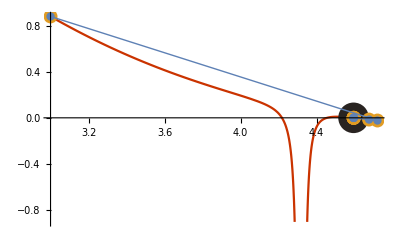

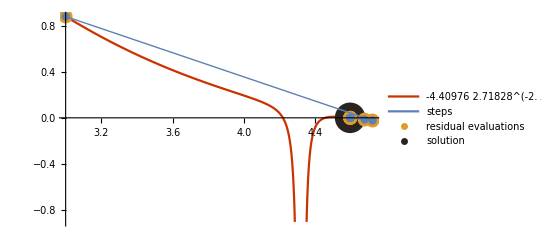

```mathematica
opts={"MaxIterations"->100};
initialGuess={3,4.72};(*{5,6}*)
newParams = {(*FernandoDuarte`LongRunRisk`Model`Parameters`psi->1.5,FernandoDuarte`LongRunRisk`Model`Parameters`gamma->8*)}
solWc=updateCoeffs[model,newParams,opts,"PrintResidualsNorm"->True,"initialGuess" -> <|"Ewc"->initialGuess|>]
plotCoeffs[model,solWc,newParams,initialGuess,opts(*,PlotLegends->Automatic*)]
plotCoeffs[model,solWc,newParams,initialGuess,opts,PlotLegends->Automatic]
```

#### PD

```mathematica
solPd=updateCoeffsPd[model["coeffsSolution"]["pd"],model["params"],{},solWc,"Epd0[1]"->5.5]
```

```mathematica
newParamStock={mud[1]->0.8*mud[1]};
updateCoeffsPd[model["coeffsSolution"]["pd"],model["params"],newParamStock,solWc,"Epd0[1]"->5]
updateCoeffsSol[model,newParamStock,{}]
```

```mathematica
newParam = {delta->0.9*delta}
updateCoeffsPd[model["coeffsSolution"]["pd"],model["params"],newParam,solWc,"Epd0[1]"->5]
updateCoeffsSol[model,newParam,{}]
```

```mathematica
updateCoeffsSol[model,newParamStock,{}]
```

```mathematica
updateCoeffsSol[model,newParamStock,{}, "MaxIterations"->1]
updateCoeffsSol[model,newParamStock,{}, "MaxIterations"->5,"CheckResiduals"->True]
```

```mathematica
updateCoeffsSol[model,newParamStock,{}, "MaxIterations"->100,"initialGuess" -> <|"Ewc"->{4.6},"Epd"->{{4.6}}|>]
```

```mathematica
updateCoeffsSol[model,{mud[1]->0.000171798971158},solWc, "MaxIterations"->200]
```

```mathematica
updateCoeffsSol[model,{mud[1]->0.000171798971158},Flatten@solPd, "MaxIterations"->200,"initialGuess" -> <|"Ewc"->{6.6},"Epd"->{{5}}|>]
```

```mathematica
updateCoeffsSol[model,{mud[1]->0.000171798971158},Flatten@Join[solWc,solPd], "MaxIterations"->200,"initialGuess" -> <|"Ewc"->{6.6},"Epd"->{{5}}|>]
```

#### Bonds

```mathematica
solBond=updateCoeffsBond[model["coeffsSolution"]["bond"],model["params"],{},12,solWc]
solNomBond=updateCoeffsBond[model["coeffsSolution"]["nombond"],model["params"],{},12,solWc]
```

```mathematica
(*coeff returns Values that are numbers*)
model=modBKY;
modelc=coeff[model];
And@@(NumberQ/@(Values@Flatten@{modelc}))
```

```mathematica
(*check maxMaturity option*)
modelMaxMaturity = coeff[model,"maxMaturity"->2];
And@@(NumberQ/@(Values@Flatten@{modelMaxMaturity}))
NumberQ[FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`R[2][0]/.modelMaxMaturity]
Not@NumberQ[FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`R[3][0]/.modelMaxMaturity]
(*check FindRoot, RecurrenceTable options*)
modelOptions = coeff[model,"maxMaturity"->2,PrecisionGoal->$MachinePrecision];
And@@(NumberQ/@(Values@Flatten@{modelOptions}))
(*pass new parameters*)
modelParam = coeff[model,"parameters"->{psi->1.3},MaxIterations->3500];
And@@(NumberQ/@(Values@Flatten@{modelParam}))
Not[(FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[1]/.modelc)===(FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[1]/.modelParam)]
```

```mathematica
(*change initial guess for solver*)
10^-8>=Plus@@(RealAbs/@(Chop[Values@coeff[model]-Values@coeff[model,"initialGuessEwc"->7]]))
10^-8>=Plus@@(RealAbs/@(Chop[Values@coeff[model]-Values@coeff[model,"initialGuessEPd"->6]]))
10^-8>=Plus@@(RealAbs/@(Chop[Values@coeff[model]-Values@coeff[model,"initialGuessEwc"->7,"initialGuessEPd"->6]]))
```

```mathematica
(*issue message and compute theta using the user-provided psi and gamma*)
Not[Values@coeff[model,"parameters"->{psi->1.3,gamma->3,theta->2}]===Values@coeff[model]]

Values@coeff[model,"parameters"->{psi->1.3,gamma->3,theta->2}]===Values@coeff[model,"parameters"->{psi->1.3,gamma->3,theta->N[(1-3)/(1-1/1.3)]}]===Values@coeff[model,"parameters"->{psi->1.3,gamma->3}]
```

```mathematica
(*provide 2 of {psi,gamma,theta}, code solves for the third one*)
Not[coeff[model,"parameters"->{psi->1.3,gamma->3}]===coeff[model]]
coeff[model,"parameters"->{psi->1.3,gamma->3}]===coeff[model,"parameters"->{psi->1.3,theta->(1-3)/(1-1/1.3)}]===coeff[model,"parameters"->{theta->(1-3)/(1-1/1.3),gamma->3}]
```

```mathematica
(*should abort*)
(*psi=1*)
coeff[model,"parameters"->{psi->1}]
(*theta without gamma or psi*)
coeff[model,"parameters"->{theta->1}]
```

```mathematica
(*provided incorrect parameters*)
coeff[model,"parameters"->{foo->1}]
```

```mathematica
modBKYc=coeff[modBKY];
```

```mathematica
modNRCc=coeff[modNRC];
```

```mathematica
(*modBSc=coeff[modBS];*)
```

```mathematica
modDESc=coeff[modDES];
```

```mathematica
(*modWCratioc=coeff[modWCratio];*)
```

```mathematica
And@@(NumberQ/@(Values@Flatten@{modBKYc,modNRCc,modDESc}))
```

```mathematica
coeff[modNRCa,"maxMaturity"->120]
```

```mathematica
processNewParameters=FernandoDuarte`LongRunRisk`ComputationalEngine`SolveEulerEq`Private`processNewParameters;
And@@Table[
And@@{
(*issue message and compute theta using the user-provided psi and gamma*)
processNewParameters[{psi->1.3,gamma->3,theta->2},model["parameters"]]==={FernandoDuarte`LongRunRisk`Model`Parameters`psi->1.3,FernandoDuarte`LongRunRisk`Model`Parameters`gamma->3,FernandoDuarte`LongRunRisk`Model`Parameters`theta->-8.666666666666664},

(*ignore user-provided theta and return theta computed using the user-provided psi and gamma*)
processNewParameters[{psi->1.3,gamma->3,theta->2},model["parameters"]]===processNewParameters[{psi->1.3,gamma->3,theta->N[(1-3)/(1-1/1.3)]},model["parameters"]],

(*provide 2 of {psi,gamma,theta}, code solves for the third one*)
Sort@processNewParameters[{psi->1.3,gamma->3},model["parameters"]]===Sort@processNewParameters[{psi->1.3,gamma->3},model["parameters"]]===Sort@processNewParameters[{theta->(1-3)/(1-1/1.3),gamma->3},model["parameters"]]==={FernandoDuarte`LongRunRisk`Model`Parameters`gamma->3,FernandoDuarte`LongRunRisk`Model`Parameters`psi->1.3,FernandoDuarte`LongRunRisk`Model`Parameters`theta->-8.666666666666664},

(*should abort*)
(*psi=1*)
CheckAbort[processNewParameters[{psi->1},model["parameters"]],True],
(*theta without gamma or psi*)
CheckAbort[processNewParameters[{theta->1},model["parameters"]],True],
(*provided incorrect parameters*)
CheckAbort[processNewParameters[{foo->1},model["parameters"]],True]
}
,
{model,{modBKY,modNRC}}]
```